## MaRIE

#### Study of the Saturation length based on Ming Xie formula

```mathematica
SaturationL[ση_,ε_,β_,λu_:1.86 10^-2,λ1_:0.3 10^-10,bEnergy_:12 10^9,Ib_:3000]:=Block[{ku,k1,γb,K,ξ,JJ,σr,IA=17050,ρ,LG0,ηγ,ηε,ηd,Λ, Pb, Psat, α, Pn},
(*
Undulator period and wavelength in meters;
Design Optimization for an X-ray Free Elecgron Laser Driven by SLAC Linac
	Design Optimization for an X-ray Free Elecgron Laser Driven by SLAC Linac
	Ming Xie,Lawrence Berkeley Laboratory,Berkeley,CA 94720,USA
	http://accelconf.web.cern.ch/AccelConf/p95/ARTICLES/TPG/TPG10.PDF
*)
ku=2π/λu;
k1=2π/λ1;
γb=1+bEnergy/510999.;
K=√2 √(2 γb^2 λ1/λu-1);
ξ=K^2/(4+2 K^2);
σr=√(ε β/γb);

JJ=BesselJ[0,ξ]-BesselJ[1,ξ];
ρ=(1/16 Ib/IA(K^2 JJ^2)/(γb^3 σr^2 ku^2))^(1/3); (*FEL parameter*)
LG0=λu/(4π √3 ρ);(*1D Gain Length*)
ηd=LG0/(2k1 σr^2);
ηε=LG0 ((4π)ε/γb)/(β λ1);
ηγ=4π LG0/λu ση;
Λ=0.45 ηd^0.57+0.55 ηε^1.6+3 ηγ^2+0.35 ηε^2.9 ηγ^2.4+51 ηd^0.95 ηγ^3+5.4 ηd^0.7 ηε^1.9+1140 ηd^2.2 ηε^2.9 ηγ^3.2;
(*Return[{4π √3 LG0(1+Λ),σr}];*)
Pb = Ib bEnergy;
Psat = 1.6 ρ Pb/(1+Λ)^2;
α=1/9;
Pn = ρ^2 bEnergy 1.60217662 10^-19 299792458/λ1;
(*Return[4π √3 LG0(1+Λ)];*)
Return[LG0(1+Λ)Log[Psat/Pn/α]];
];
```

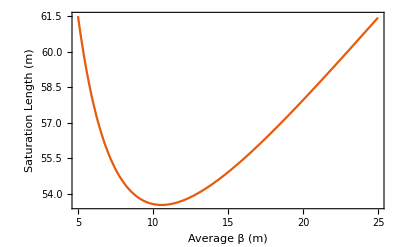

```mathematica
Plot[SaturationL[1.5 10^-4,0.2 10^-6,x], {x,5,25},FrameLabel->{"Average β (m)","Saturation Length (m)"},LabelStyle->{FontFamily->"Times",14,GrayLevel[0]},PlotTheme->"Scientific"]
```

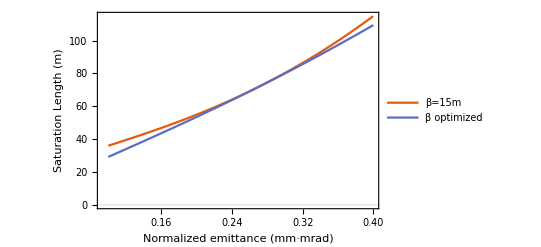

```mathematica
data1=Table[{x,SaturationL[1.5 10^-4,x 10^-6,15]},{x,100 10^-3,400 10^-3,10^-2}];
data2=Table[{x,FindMinimum[{SaturationL[1.5 10^-4,x 10^-6,β],0<β<50},{β,30}][[1]]},{x,100. 10^-3,400 10^-3,10^-2}];
ListLinePlot[{data1,data2},FrameLabel->{"Normalized emittance (mm·mrad)","Saturation Length (m)"},LabelStyle->{FontFamily->"Times",14,GrayLevel[0]},PlotTheme->"Scientific",PlotLegends->Placed[LineLegend[{"β=15m","β optimized"},Joined->True],{Left,Top}]]
```

```mathematica
FindMinimum[{SaturationL[1.5 10^-4,0.2 10^-6,β],0<β<25},{β,15}]
GL=%[[1]]/(4π √3)/0.0186
σr=10^6 √(0.2 10^-6 (15)/(1+12 10^9/510999.))
```

{53.5388,{β→10.572}}

132.247

11.3024

We can see that in the range of our emittance a fixed β function performs relatively well.

#### Study of the coherence length based on Ming Xie formula

```mathematica
CoherenceL[ση_,ε_,β_,Ib_:3000,λu_:1.86 10^-2,λ1_:0.3 10^-10,bEnergy_:12 10^9]:=Block[{Lsat},
(*
Undulator period and wavelength in meters;

*)
Lsat = SaturationL[ση, ε, β, λu, λ1,bEnergy,Ib];
Return[1/(2 √π)λ1/λu Lsat];
];
```

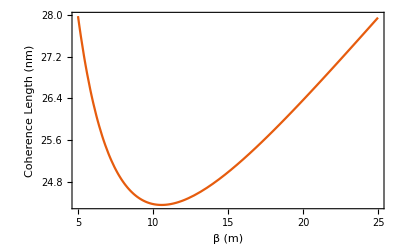

{24.3597,{β→10.572}}

```mathematica
Plot[10^9 CoherenceL[1.5 10^-4,0.2 10^-6,β],{β,5,25},FrameLabel->{"β (m)","Coherence Length (nm)"},LabelStyle->{FontFamily->"Times",14,GrayLevel[0]},PlotTheme->"Scientific"]
FindMinimum[10^9 CoherenceL[1.5 10^-4,0.2 10^-6,β],{β,10}]
```

The slippage length:

```mathematica
2 √π CoherenceL[1.5 10^-4,0.2 10^-6,12.13836378915493]
2 √π CoherenceL[1.5 10^-4,0.2 10^-6,18.3149]
(1+2 √π)CoherenceL[1.5 10^-4,0.2 10^-6,18.3149]
```

8.67109×10^-8

9.16936×10^-8

1.1756×10^-7

Current reduction by 50% results in lengthening coherence length by 50%

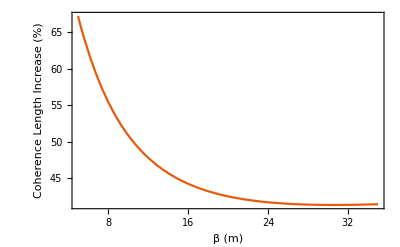

43.1232

```mathematica
Plot[-100+100CoherenceL[1.5 10^-4,0.2 10^-6,β,3000*0.5]/CoherenceL[1.5 10^-4,0.2 10^-6,β,3000],{β,5,35},FrameLabel->{"β (m)","Coherence Length Increase (%)"},LabelStyle->{FontFamily->"Times",14,GrayLevel[0]},PlotTheme->"Scientific"]
-100+100CoherenceL[1.5 10^-4,0.2 10^-6,18.3149,3000*0.5]/CoherenceL[1.5 10^-4,0.2 10^-6,18.3149,3000]
```

```mathematica
PowerGW[ση_,ε_,β_,λu_:1.86 10^-2,λ1_:0.3 10^-10,bEnergy_:12 10^9,Ib_:3000,q_:100 10^-12]:=Block[{ku,k1,γb,K,ξ,JJ,σr,IA=17050,ρ,LG0,ηγ,ηε,ηd,Λ,τ=q/Ib,P},
(*
Undulator period and wavelength in meters;
0.3 10^-10 wavelength corresponds to 6.62×10^-15 J energy
*)
ku=2π/λu;
k1=2π/λ1;
γb=1+bEnergy/510999.;
K=√2 √(2 γb^2 λ1/λu-1);
ξ=K^2/(4+2 K^2);
σr=√(ε β/γb);

JJ=BesselJ[0,ξ]-BesselJ[1,ξ];
ρ=(1/16 Ib/IA(K^2 JJ^2)/(γb^3 σr^2 ku^2))^(1/3); (*FEL parameter*)
LG0=λu/(4π √3 ρ);(*1D Gain Length*)
ηd=LG0/(2k1 σr^2);
ηε=LG0 ((4π)ε/γb)/(β λ1);
ηγ=4π LG0/λu ση;
Λ=0.45 ηd^0.57+0.55 ηε^1.6+3 ηγ^2+0.35 ηε^2.9 ηγ^2.4+51 ηd^0.95 ηγ^3+5.4 ηd^0.7 ηε^1.9+1140 ηd^2.2 ηε^2.9 ηγ^3.2;
(*Return[{4π √3 LG0(1+Λ),σr}];*)
P=1.6/(1+Λ)^2 ρ bEnergy Ib;
Return[P 10^-9];
];
```

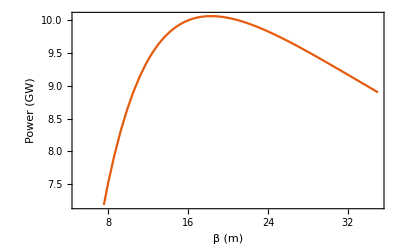

{10.0596,{β→18.3149}}

```mathematica
Plot[PowerGW[1.5 10^-4,0.2 10^-6,β],{β,5,35},FrameLabel->{"β (m)","Power (GW)"},LabelStyle->{FontFamily->"Times",14,GrayLevel[0]},PlotTheme->"Scientific"]
FindMaximum[PowerGW[1.5 10^-4,0.2 10^-6,β],{β,20}]
```

```mathematica
PhotonNumber[ση_,ε_,β_,λu_:1.86 10^-2,λ1_:0.3 10^-10,bEnergy_:12 10^9,Ib_:3000,q_:100 10^-12]:=Block[{ku,k1,γb,K,ξ,JJ,σr,IA=17050,ρ,LG0,ηγ,ηε,ηd,Λ,τ=q/Ib,P},
(*
Undulator period and wavelength in meters;
0.3 10^-10 wavelength corresponds to 6.62×10^-15 J energy
*)
ku=2π/λu;
k1=2π/λ1;
γb=1+bEnergy/510999.;
K=√2 √(2 γb^2 λ1/λu-1);
ξ=K^2/(4+2 K^2);
σr=√(ε β/γb);

JJ=BesselJ[0,ξ]-BesselJ[1,ξ];
ρ=(1/16 Ib/IA(K^2 JJ^2)/(γb^3 σr^2 ku^2))^(1/3); (*FEL parameter*)
LG0=λu/(4π √3 ρ);(*1D Gain Length*)
ηd=LG0/(2k1 σr^2);
ηε=LG0 ((4π)ε/γb)/(β λ1);
ηγ=4π LG0/λu ση;
Λ=0.45 ηd^0.57+0.55 ηε^1.6+3 ηγ^2+0.35 ηε^2.9 ηγ^2.4+51 ηd^0.95 ηγ^3+5.4 ηd^0.7 ηε^1.9+1140 ηd^2.2 ηε^2.9 ηγ^3.2;
(*Return[{4π √3 LG0(1+Λ),σr}];*)
P=1.6/(1+Λ)^2 ρ bEnergy Ib;
Return[P τ/(6.62×10^-15)];
];
```

```mathematica
PhotonNumber[1.5 10^-4,0.2 10^-6,12.13836378915493]
FindMaximum[PhotonNumber[1.5 10^-4,0.2 10^-6,β],{β,15}]
σr=10^6 √(0.2 10^-6 (18.3149)/(1+12 10^9/510999.))
```

4.74624×10^10

{5.06527×10^10,{β→18.3149}}

12.489

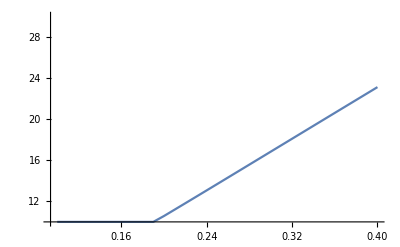

```mathematica
g3=ListLinePlot[Table[{x 10^6,β/.FindMinimum[{SaturationL[1.5 10^-4,x,β],10<β<50},{β,30}][[2]]},{x,100 10^-9,400 10^-9,10^-8}],PlotRange->{10,30},PlotLegends->"Gain Length optimization"]
```

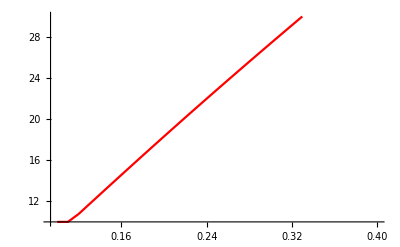

```mathematica
g4=ListLinePlot[Table[{x 10^6,β/.FindMaximum[{PhotonNumber[1.5 10^-4,x,β],10<β<50},{β,30}][[2]]},{x,100 10^-9,400 10^-9,10^-8}],PlotStyle->Red,PlotRange->{10,30},PlotLegends->"Photon Number optimization"]
```

OptionValue::nodef: Unknown option PlotLegends for Graphics.

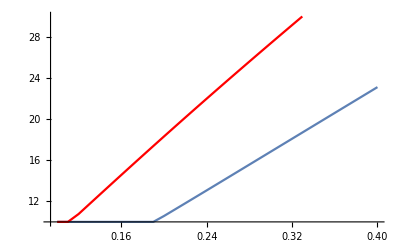

```mathematica
Show[{g3,g4},PlotLegends->{"Gain Length optimization","Photon Number optimization"}]
```

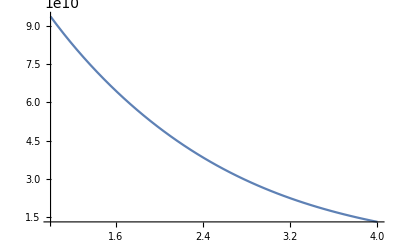

```mathematica
g5=Plot[PhotonNumber[1.5 10^-4,x,15],{x,100 10^-9,400 10^-9}]
```

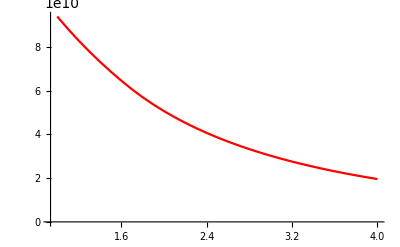

```mathematica
g6=ListLinePlot[Table[{x,FindMaximum[{PhotonNumber[1.5 10^-4,x,β],15<β<50},{β,30}][[1]]},{x,100 10^-9,400 10^-9,10^-8}],PlotStyle->Red]
```

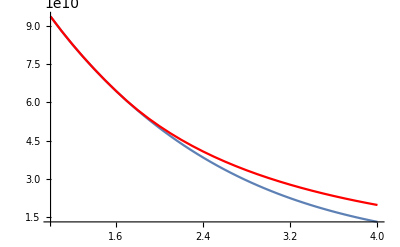

```mathematica
Show[{g5,g6}]
```

```mathematica
SigmaR[ε_,β_,bEnergy_:12 10^9]:=Block[{γb,σr},
(*
Undulator period and wavelength in meters;
0.3 10^-10 wavelength corresponds to 6.62×10^-15 J energy
*)
γb=1+bEnergy/510999.;
σr=√(ε β/γb);

Return[σr];
];
```

```mathematica
10^6 SigmaR[2 10^-7,18.3149]
10^6 SigmaR[2 10^-7,15]
10^6 SigmaR[2 10^-7,12.13836378915493]
SaturationL[1.5 10^-4,0.2 10^-6,18.3149]
```

12.489

11.3024

10.1673

56.85

#### The study of the photon number based on Ming Xie formula in a fixed length undulator

```mathematica
LimitedPhotonNumber[ση_,ε_,β_,Ib_:3000,λu_:1.86 10^-2,λ1_:0.3 10^-10,bEnergy_:12 10^9,q_:100 10^-12,undulatorL_:77]:=Block[{ku,k1,γb,K,ξ,JJ,σr,IA=17050,ρ,LG0,LG,ηγ,ηε,ηd,Λ,τ=q/Ib,P,limit,Pb, Psat, α, Pn, Lsat},
(*
Undulator period and wavelength in meters;
0.3 10^-10 wavelength corresponds to 6.62×10^-15 J energy
*)
ku=2π/λu;
k1=2π/λ1;
γb=1+bEnergy/510999.;
K=√2 √(2 γb^2 λ1/λu-1);
ξ=K^2/(4+2 K^2);
σr=√(ε β/γb);

JJ=BesselJ[0,ξ]-BesselJ[1,ξ];
ρ=(1/16 Ib/IA(K^2 JJ^2)/(γb^3 σr^2 ku^2))^(1/3); (*FEL parameter*)
LG0=λu/(4π √3 ρ);(*1D Gain Length*)
ηd=LG0/(2k1 σr^2);
ηε=LG0 ((4π)ε/γb)/(β λ1);
ηγ=4π LG0/λu ση;
Λ=0.45 ηd^0.57+0.55 ηε^1.6+3 ηγ^2+0.35 ηε^2.9 ηγ^2.4+51 ηd^0.95 ηγ^3+5.4 ηd^0.7 ηε^1.9+1140 ηd^2.2 ηε^2.9 ηγ^3.2;
LG=LG0(1+Λ);
Pb = Ib bEnergy;
Psat = 1.6 ρ Pb/(1+Λ)^2;
α=1/9;
Pn = ρ^2 bEnergy 1.60217662 10^-19 299792458/λ1;
(*Return[4π √3 LG0(1+Λ)];*)
Lsat=LG0(1+Λ)Log[Psat/Pn/α];
If[Lsat<undulatorL,limit=1,limit=ⅇ^((undulatorL-Lsat)/LG)];
P=(1.6 limit)/(1+Λ)^2 ρ bEnergy Ib;
Return[P τ/(6.62×10^-15)];
];
```

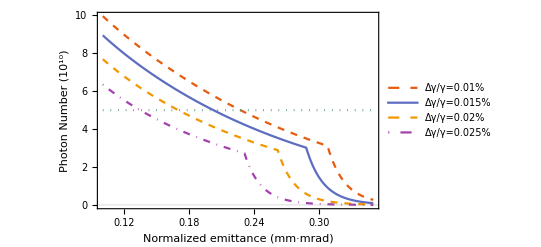

```mathematica
Plot[{10^-10 LimitedPhotonNumber[1. 10^-4,x 10^-6,18.3149],
10^-10 LimitedPhotonNumber[1.5 10^-4,x 10^-6,18.3149],
10^-10 LimitedPhotonNumber[2 10^-4,x 10^-6,18.3149],
10^-10 LimitedPhotonNumber[2.5 10^-4,x 10^-6,18.3149],
10^-10 Evaluate[y=5 10^10]},
{x,100 10^-3,350 10^-3},PlotStyle->{Dashed,Automatic,Dashed,DotDashed,Dotted},FrameLabel->{"Normalized emittance (mm·mrad)","Photon Number (10^10)"},LabelStyle->{FontFamily->"Times",14,GrayLevel[0]},
PlotTheme->"Scientific",PlotLegends->Placed[LineLegend[{"Δγ/γ=0.01%","Δγ/γ=0.015%","Δγ/γ=0.02%","Δγ/γ=0.025%"},Joined->True],{Right,Top}]]
```

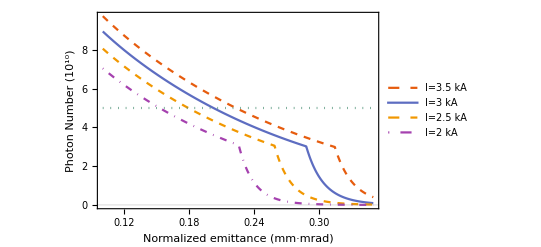

```mathematica
Plot[{10^-10 LimitedPhotonNumber[1.5 10^-4,x 10^-6,18.3149,3500],10^-10 LimitedPhotonNumber[1.5 10^-4,x 10^-6,18.3149,3000],
10^-10 LimitedPhotonNumber[1.5 10^-4,x 10^-6,18.3149,2500],
10^-10 LimitedPhotonNumber[1.5 10^-4,x 10^-6,18.3149,2000], Evaluate[y=5]},{x,100 10^-3,350 10^-3},
FrameLabel->{"Normalized emittance (mm·mrad)","Photon Number (10^10)"},LabelStyle->{FontFamily->"Times",14,GrayLevel[0]},
PlotStyle->{Dashed,Automatic,Dashed,DotDashed,Dotted},PlotTheme->"Scientific",PlotLegends->Placed[LineLegend[{"I=3.5 kA","I=3 kA","I=2.5 kA","I=2 kA"},Joined->True],{Right,Top}]]
```

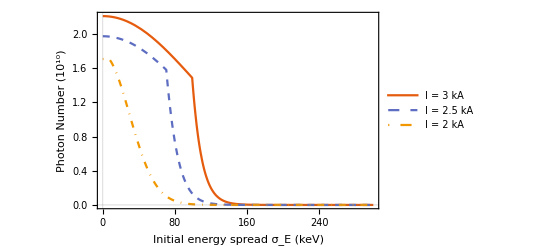

```mathematica
Plot[{
0.88 0.385159 10^-10 LimitedPhotonNumber[((21.8+1)x)/(12 10^6),0.2 10^-6,18.3149,3000],
0.88 0.385159 10^-10 LimitedPhotonNumber[((21.8+1)x)/(12 10^6),0.2 10^-6,18.3149,2500],
0.88 0.385159 10^-10 LimitedPhotonNumber[((21.8+1)x)/(12 10^6),0.2 10^-6,18.3149,2000]},
{x,0.,300},
PlotStyle->{Automatic,Dashed,DotDashed},FrameLabel->{"Initial energy spread σ_E (keV)","Photon Number (10^10)"},LabelStyle->{FontFamily->"Times",14,GrayLevel[0]},
PlotTheme->"Scientific",PlotLegends->Placed[LineLegend[{"I = 3 kA", "I = 2.5 kA", "I = 2 kA"},Joined->True],{Right,Top}]]
```

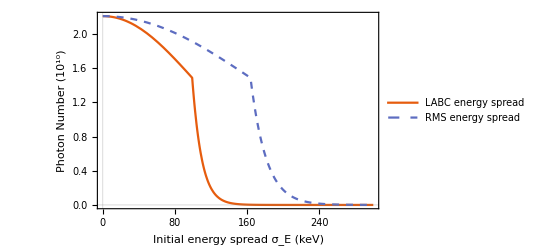

```mathematica
Plot[{
0.88 0.385159 10^-10 LimitedPhotonNumber[((21.8+1)x)/(12 10^6),0.2 10^-6,18.3149],
0.88 0.385159 10^-10 LimitedPhotonNumber[(13.8x)/(12 10^6),0.2 10^-6,18.3149]},
{x,0.,300},
PlotStyle->{Automatic,Dashed,Dotted},FrameLabel->{"Initial energy spread σ_E (keV)","Photon Number (10^10)"},LabelStyle->{FontFamily->"Times",14,GrayLevel[0]},
PlotTheme->"Scientific",PlotLegends->Placed[LineLegend[{"LABC energy spread", "RMS energy spread"},Joined->True],{Right,Top}]]
```

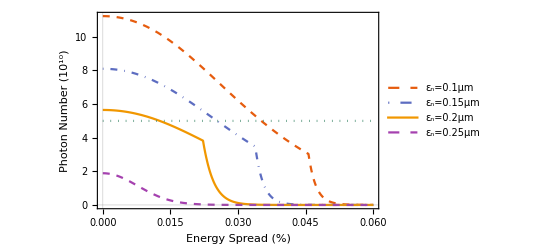

```mathematica
Plot[{
10^-10 LimitedPhotonNumber[x 10^-2,0.1 10^-6,12.13836378915493],
10^-10 LimitedPhotonNumber[x 10^-2,0.15 10^-6,12.13836378915493],
10^-10 LimitedPhotonNumber[x 10^-2,0.2 10^-6,12.13836378915493],
10^-10 LimitedPhotonNumber[x 10^-2,0.25 10^-6,12.13836378915493],
10^-10 Evaluate[y=5 10^10]},
{x,0.,6 10^-2},
PlotStyle->{Dashed,DotDashed,Automatic,Dashed,Dotted},FrameLabel->{"Energy Spread (%)","Photon Number (10^10)"},LabelStyle->{FontFamily->"Times",14,GrayLevel[0]},
PlotTheme->"Scientific",PlotLegends->Placed[LineLegend[{"ε_n=0.1μm","ε_n=0.15μm","ε_n=0.2μm","ε_n=0.25μm"},Joined->True],{Right,Top}]]
```

```mathematica
Plot[{
10^-10 LimitedPhotonNumber[x 10^-2,0.1 10^-6,12.13836378915493],
10^-10 LimitedPhotonNumber[x 10^-2,0.15 10^-6,12.13836378915493],
10^-10 LimitedPhotonNumber[x 10^-2,0.2 10^-6,12.13836378915493],
10^-10 LimitedPhotonNumber[x 10^-2,0.25 10^-6,12.13836378915493],
10^-10 Evaluate[y=5 10^10]},
{x,0.,6 10^-2},
PlotStyle->{Dashed,DotDashed,Automatic,Dashed,Dotted},FrameLabel->{"Energy Spread (%)","Photon Number (10^10)"},LabelStyle->{FontFamily->"Times",14,GrayLevel[0]},
PlotTheme->"Scientific",PlotLegends->Placed[LineLegend[{"ε_n=0.1μm","ε_n=0.15μm","ε_n=0.2μm","ε_n=0.25μm"},Joined->True],{Right,Top}]]
```

-Graphics-